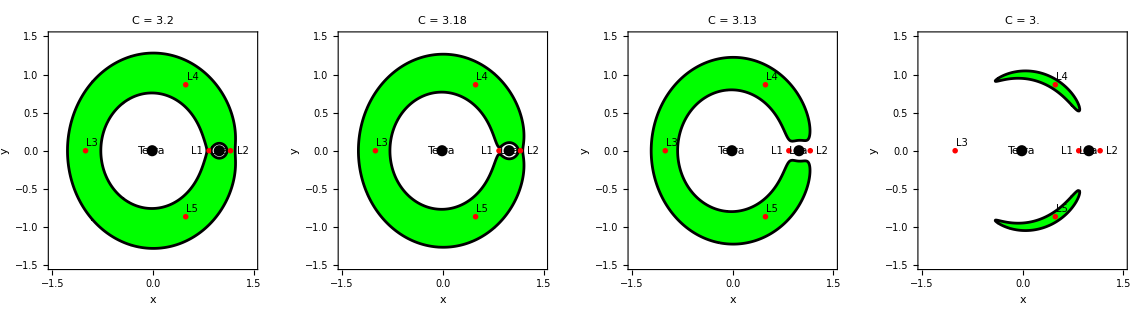

```mathematica
mu=0.01215;

r1[x_,y_]:=Sqrt[(x+mu)^2+y^2];
r2[x_,y_]:=Sqrt[(x-(1-mu))^2+y^2];
U[x_,y_]:=(x^2+y^2)+2*(1-mu)/r1[x,y]+2*mu/r2[x,y];

Cvalores={3.2,3.18,3.13,3.0};


L1={x/. FindRoot[x-(1-mu)/((x+mu)^2)+mu/((x-(1-mu))^2)==0,{x,0.5}],0};
L2={x/. FindRoot[x-(1-mu)/((x+mu)^2)-mu/((x-(1-mu))^2)==0,{x,1.5}],0};
L3={x/. FindRoot[x+(1-mu)/((x+mu)^2)+mu/((x-(1-mu))^2)==0,{x,-1}],0};
L4={0.5-mu,Sqrt[3]/2};
L5={0.5-mu,-Sqrt[3]/2};


GraphicsGrid[Partition[Table[RegionPlot[U[x,y]<=Cvalor,{x,-1.5,1.5},{y,-1.5,1.5},PlotPoints->50,MaxRecursion->3,BoundaryStyle->Black,FrameLabel->{"x","y"},PlotLabel->Style[StringForm["C = ``",Cvalor],10,Bold],PlotStyle->Green,Epilog->{{Black,PointSize[0.02],Point[{{-mu,0},{1-mu,0}}]},{Red,PointSize[0.01],Point[{L1,L2,L3,L4,L5}]},Text[Style["L1",10],L1+{-0.18,0}],Text[Style["L2",10],L2+{0.18,0}],Text[Style["L3",10],L3+{0.1,0.1}],Text[Style["L4",10],L4+{0.1,0.1}],Text[Style["L5",10],L5+{0.1,0.1}],Text[Style["Terra",11],{-mu,0},{0,2}],Text[Style["Lua",11],{1-mu,0},{0,2}]}],{Cvalor,Cvalores}],4],ImageSize->Large]
```